Import podatkov ter obdelava za matematiko

```mathematica
normData[data_]:=Transpose[{data[[All,1]],data[[All,2]]/data[[1,2]]}]
```

```mathematica
data=Import["~/Work/ElektroShag/crt/pointsrelations.csv","CSV","FieldSeparators"->","];data=ToExpression@Table[StringReplace[data[[i,j]],{"("->"{",")"->"}"}],{i,Length@data},{j,Length@data[[1]]}];data=Table[normData[data[[i]]],{i,Length@data}];
```

Transformacija podatkova da dobimo oddaljenost iz odziva (uporabil sem prvo metodo)

```mathematica
transformddata[data_]:=Transpose[{data[[All,1]],(data[[All,2]]^-1-data[[1,2]]^-1)/(data[[-1,2]]^-1-data[[1,2]]^-1)}]
```

```mathematica
transformddata[data_]:=Transpose[{data[[All,1]],(data[[All,2]]^-1-1)}]
```

```mathematica
trdata=Table[transformddata[data[[i]]],{i,Length@data}];
```

Uporabim simulacije, pri katerih se je dogodek zgodil poleg noda

```mathematica
dataAll={trdata[[5]],trdata[[7]],trdata[[1]]};
```

```mathematica
dataAll
```

{{{1,0.},{14,0.12922},{13,0.130018},{8,0.178103},{10,0.334522},{11,0.436172},{7,0.471526},{5,0.587842},{4,0.601799},{3,0.617005},{12,0.641691},{6,0.677},{9,0.769541},{15,0.900718},{2,1.}},{{2,0.},{15,0.329346},{10,0.354423},{9,0.370503},{4,0.424112},{12,0.429872},{5,0.496406},{6,0.496423},{3,0.559342},{13,0.586614},{14,0.588002},{11,0.62715},{7,0.627411},{8,0.665935},{1,1.}},{{4,0.},{12,0.311292},{2,0.402332},{7,0.461121},{11,0.483546},{3,0.525265},{5,0.543295},{9,0.564408},{6,0.585116},{15,0.637289},{1,0.690364},{14,0.817459},{13,0.829478},{8,0.888645},{10,1.}}}

Izacunamo 3 zacetne tocke, za katere je natancnost najvecja

```mathematica
pointsVal=ConstantArray[{0,0},15];
pointsVal[[1]]={0,0};
pointsVal[[2]]={dataAll[[1,-1,2]],0};
pointsVal[[4]]={x,y}/.Solve[{x^2+y^2==dataAll[[3,11,2]]^2,(x-pointsVal[[2,1]])^2+y^2==dataAll[[2,5,2]]^2},{x,y}][[2]]//Quiet
```

{0.648366,0.237117}

ostale tocke izracunamo glede na te tri tocke, v prvem primeru na N1-N2, drugem N1-N4, v zadnjem v N2-N4

```mathematica
sol3=Block[{i,out={},p1=1,p2=2,p3=4},For[i=1,i≤15,i++,If[i==p1||i==p2||i==p3,Continue[]];
Block[{dis1,dis2,dis3,pos1,pos2,pos3},
pos1=Position[dataAll[[1]],i][[1,1]];
pos2=Position[dataAll[[2]],i][[1,1]];
pos3=Position[dataAll[[3]],i][[1,1]];
dis1=dataAll[[1,pos1,2]];dis2=dataAll[[2,pos2,2]];dis3=dataAll[[3,pos3,2]];AppendTo[out,{x,y}/.Solve[{x^2+y^2==dis1,(x-pointsVal[[p3,1]])^2+(y-pointsVal[[p3,2]])^2==dis3},{x,y}]]]];out]//Quiet;sol2=Block[{i,out={},p1=1,p2=2,p3=4},For[i=1,i≤15,i++,If[i==p1||i==p2||i==p3,Continue[]];
Block[{dis1,dis2,dis3,pos1,pos2,pos3},
pos1=Position[dataAll[[1]],i][[1,1]];pos2=Position[dataAll[[2]],i][[1,1]];pos3=Position[dataAll[[3]],i][[1,1]];
dis1=dataAll[[1,pos1,2]];dis2=dataAll[[2,pos2,2]];dis3=dataAll[[3,pos3,2]];AppendTo[out,{x,y}/.Solve[{x^2+y^2==dis1,(x-pointsVal[[p2,1]])^2+(y-pointsVal[[p2,2]])^2==dis2},{x,y}]]]];out]//Quiet;sol1=Block[{i,out={},p1=1,p2=2,p3=4},For[i=1,i≤15,i++,If[i==p1||i==p2||i==p3,Continue[]];
Block[{dis1,dis2,dis3,pos1,pos2,pos3},
pos1=Position[dataAll[[1]],i][[1,1]];pos2=Position[dataAll[[2]],i][[1,1]];
pos3=Position[dataAll[[3]],i][[1,1]];
dis1=dataAll[[1,pos1,2]];dis2=dataAll[[2,pos2,2]];dis3=dataAll[[3,pos3,2]];AppendTo[out,{x,y}/.Solve[{(x-pointsVal[[p2,1]])^2+(y-pointsVal[[p2,2]])^2==dis2,(x-pointsVal[[p3,1]])^2+(y-pointsVal[[p3,2]])^2==dis3},{x,y}]]]];out]//Quiet;
```

Izvecemo tocke

```mathematica
pointsVal[[3]]=sol1[[All,2]][[1]];
Table[pointsVal[[i+3]]=sol1[[All,2]][[i]],{i,2,12}];
pointsValR1a=pointsVal;
```

```mathematica
pointsVal[[3]]=sol2[[All,2]][[1]];
Table[pointsVal[[i+3]]=sol2[[All,2]][[i]],{i,2,12}];
pointsValR2b=pointsVal;
```

```mathematica
pointsVal[[3]]=sol3[[All,2]][[1]];
Table[pointsVal[[i+3]]=sol3[[All,2]][[i]],{i,2,12}];
pointsValR3b=pointsVal;
```

```mathematica
pointsVal
```

{{-0.394909,0.838374},{-0.352574,0.334973},{0.357048,0.781903},{-0.14148-0.19169 ⅈ,-0.19169+0.14148 ⅈ},{0.519231-0.101082 ⅈ,0.703504+0.0746051 ⅈ},{-0.199587,0.868262},{0.0246096,0.562631},{-0.538965,0.782831},{-0.303477,0.814499},{0,0},{0.748735,0},{-0.333703,0.347577},{-0.486532,0.798681},{0.444626,0.602422},{-0.410464,0.791545}}

```mathematica
sol2[[All,2]]
```

{{0.917523,-0.130286},{0.424004,-0.238192},{0.641947,0.571629},{-0.14148+0.19169 ⅈ,-0.19169-0.14148 ⅈ},{0.519231+0.101082 ⅈ,0.703504-0.0746051 ⅈ},{0.888519,0.0651689},{0.530388,0.189333},{0.906903,-0.284314},{0.867762,-0.0499519},{0.430487,-0.216444},{0.906596,-0.229538},{0.877359,-0.158952}}

Izbira tock je ena izmed resitev. Dalo bi se narediti boljsi priblizek

```mathematica
plotLabPo[pointset_]:=Table[Graphics[Text["N"<>ToString[i],{pointset[[i]][[1]],pointset[[i]][[2]]-0.05}]],{i,Length@pointset}]
```

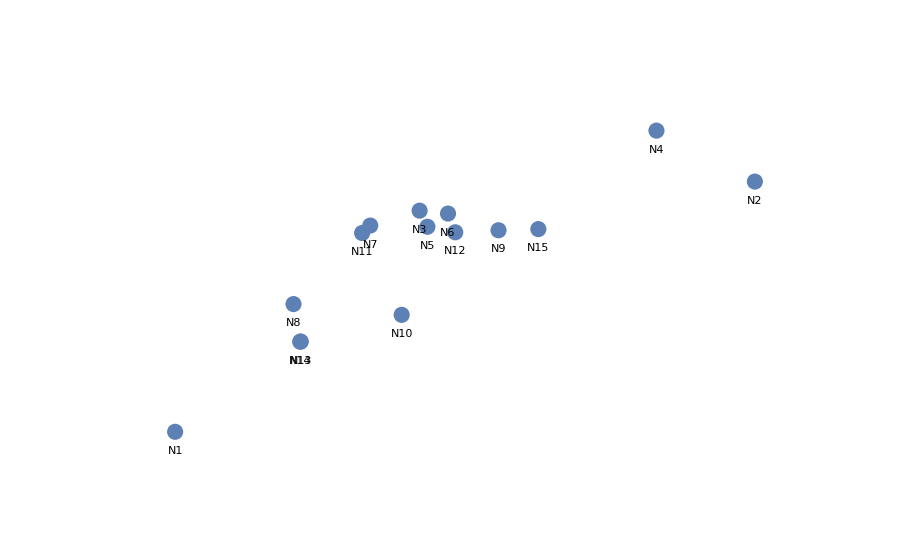

```mathematica
Show[ListPlot[{pointsValR2b},Axes->False,Frame->None,PlotRange->{{-0.2,1.4},{-0.2,1.0}}],plotLabPo[pointsValR2b]]
```

```mathematica
Export[NotebookDirectory[]<>"points.txt",pointsValR2b]
```

/home/crt/Work/ElektroShag/crt/points.txt